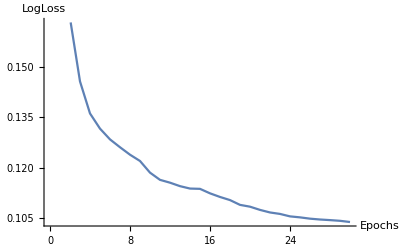

```mathematica
ListPlot[{0.21736082041368,0.16466593604361,0.14576125033834,0.13617665090418,0.1316316685428,0.12841140109579,0.12606091145277,0.12383231803081,0.12195101114244,0.118463829382,0.11630609242456,0.11545915542115,0.11442015904699,0.11369985508871,0.11361383928296,0.11227151415561,0.11118758903735,0.11025239209804,0.10881998989622,0.10827811277537,0.10731764504425,0.10654769723064,0.1061107410746,0.10537670111843,0.10508213666652,0.10469199039741,0.10443951669107,0.10425971672678,0.10405020211297,0.10369061594913},Joined->True,AxesLabel->{"Epochs","LogLoss"}]
```

```mathematica
training={1.1857037077878,1.1568920434748,1.1382533877402,1.1320226926801,1.1282733139864,1.1284307928981,1.1277204329819,1.1238634572395,1.1266416395118,1.1228654436857,1.1155310884047,1.1181081017557,1.1139795633822,1.1067718312007,1.1123107485911,
1.1136764559083,1.1112731467518,1.1074643421733,1.1070344890995,1.1040645725064,1.1044125557868,1.1084801420224,1.1050272875968,1.1040373857576,1.1033446787101,1.1032790698347,1.1062664158515,1.0994833508158,1.1019257409033,1.1002191199975
}
valid={1.1987853601282,1.166994443358,1.1531033142155,1.1506587734719,1.1497900349951,1.1461527631988,1.145564341323,1.1407726176273,1.1408644600486,1.1418396428289,1.1365927728545,1.1342934548712,
1.1345604389202,1.1302555383774,1.1324764042634,
1.1351975998186,1.1312851068994,1.1321948271227,1.1295509267027,1.1301780746687,1.1282251810101,1.1316425129556,1.1332250851359,1.12688044000621,1.1281262821813,1.1248091134433,
1.1304958990638,1.1247877414055,1.1266780479107,1.1264737686366
}
```

{1.1857,1.15689,1.13825,1.13202,1.12827,1.12843,1.12772,1.12386,1.12664,1.12287,1.11553,1.11811,1.11398,1.10677,1.11231,1.11368,1.11127,1.10746,1.10703,1.10406,1.10441,1.10848,1.10503,1.10404,1.10334,1.10328,1.10627,1.09948,1.10193,1.10022}

{1.19879,1.16699,1.1531,1.15066,1.14979,1.14615,1.14556,1.14077,1.14086,1.14184,1.13659,1.13429,1.13456,1.13026,1.13248,1.1352,1.13129,1.13219,1.12955,1.13018,1.12823,1.13164,1.13323,1.12688,1.12813,1.12481,1.1305,1.12479,1.12668,1.12647}

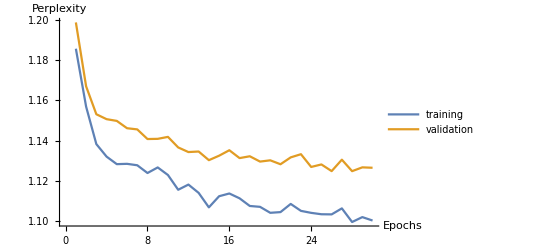

```mathematica
ListPlot[{training,valid},Joined->True,AxesLabel->{"Epochs","Perplexity"},PlotLegends->{"training","validation"}]
```

{0.340007,1972.96,4146.06,6068.89,7670.41,9264.02,10570.5,11845.7,13118.5,14392.9,15667.8}

{1.01686,648.908,1210.28,1764.48,2317.13,2868.35,3421.19,3972.87,4523.99,5075.89,5627.19,6204.31,6791.87,7406.37,8038.2,8669.89,9336.53,9977.06,10627.,11282.,11954.3,12610.,13264.3,13904.8,14549.9,15202.8}

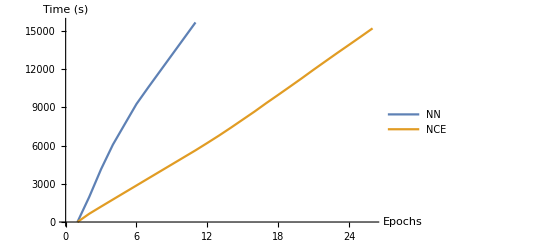

```mathematica
time1={0.340007,1972.960729,4146.064104,6068.886786,7670.408403,9264.019387,10570.450595,11845.6814,13118.480352,14392.864943,15667.840405}
time2={1.016862,648.907839,1210.283053,1764.477531,2317.129896,2868.351556,3421.191054,3972.868033,4523.99493,5075.892122,5627.191652,6204.312967,6791.868471,7406.374799,8038.204507,8669.889009,9336.529328,9977.061593,10626.978516,11282.036048,11954.256439,12610.011233,13264.258413,13904.802807,14549.938194,15202.81923}
ListPlot[{time1,time2},Joined->True,AxesLabel->{"Epochs","Time (s)"},PlotLegends->{"NN","NCE"}]
```

{8.00209,3.87684,3.67779,3.54559,3.4448,3.36798,3.30225,3.24753,3.20046,3.15975,3.12263,3.0902,3.05869,3.03267,3.00847,2.98679,2.96608,2.94798,2.93078,2.91409,2.90073}

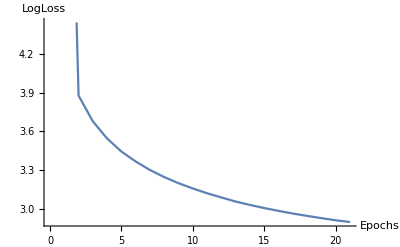

```mathematica
list={8.0020912630873,3.8768386127593,3.6777921836448,3.5455920167494,3.4448045738013,3.367984651611,3.3022470451279,3.2475326251567,3.2004648969847,3.1597451825345,3.1226270307284,3.0901990602353,3.0586857077619,3.032670014797,3.008469303226,2.9867850853402,2.9660801744208,2.9479811369658,2.9307783907003,2.9140854749776,2.9007321260614}
ListPlot[{list},Joined->True,AxesLabel->{"Epochs","LogLoss"}]
```